# PhD thesis figures

## Intro

### Wavefunction of linear resonators

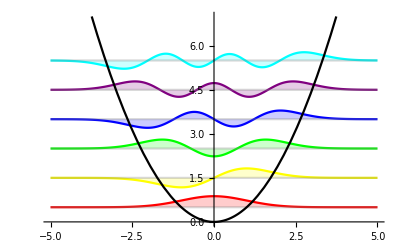

```mathematica
Energy[n_]:=(2 n+1) ℏ/2 ω;

ψ[z_,n_]:=1/2 1/Sqrt[2^n n!] ((m ω)/(π ℏ))^(1/4)Exp[-((m ω z^2)/(2 ℏ))] HermiteH[n,Sqrt[(m ω)/ℏ] z];

m=1;
ω=1;
ℏ=UnitConvert[Quantity[1,"PlanckConstant"],"SIBase"];
ℏ=QuantityMagnitude[ℏ];
ℏ=1;

Plot[{Evaluate@Table[Energy[n]+ψ[z,n],{n,0,5}],Evaluate@Table[Energy[n],{n,0,5}],z^2/2},{z,-5,5},PlotRange->{0,7},PlotStyle->Join[{Red,Yellow,Green,Blue,Purple,Cyan},Table[{Gray,Opacity[0.3]},{n,0,5}],{Black}],Filling->Table[n->Energy[n-1],{n,1,6}]]
```

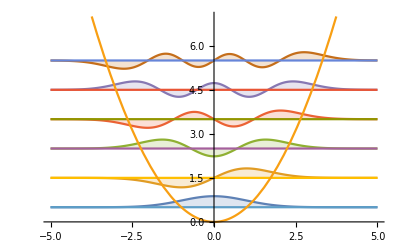

```mathematica
Plot[{Evaluate@Table[Energy[n]+ψ[z,n],{n,0,5}],Evaluate@Table[Energy[n],{n,0,5}],z^2/2},{z,-5,5},PlotRange->{0,7},Filling->Table[n->Energy[n-1],{n,1,6}]]
```

Working in the phase base we want to solve Schrodinger equation

```mathematica
sol=DSolve[4 Ec(-ψ''[ϕ]+ⅈ ng ψ'[ϕ]+ng^2 ψ[ϕ])-Ej Cos[ϕ]ψ[ϕ]==Erg ψ[ϕ], ψ[ϕ],ϕ]
```

{{ψ[ϕ]→ⅇ^((ⅈ ng ϕ)/2) C[1] MathieuC[-(-Erg+3 Ec ng^2)/Ec,-Ej/(2 Ec),ϕ/2]+ⅇ^((ⅈ ng ϕ)/2) C[2] MathieuS[-(-Erg+3 Ec ng^2)/Ec,-Ej/(2 Ec),ϕ/2]}}

```mathematica
rulesTransmon={ng->0, Ej->10, Ec->0.25}
```

{ng→0,Ej→10,Ec→0.25}

```mathematica
ψ[ϕ]/.sol/.rulesTransmon
```

{C[1] MathieuC[-4. (0.-Erg),-20.,ϕ/2]+C[2] MathieuS[-4. (0.-Erg),-20.,ϕ/2]}

### Resonators in waveguides

```mathematica
ColorData[97,"ColorList"][[1]]
```

RGBColor[0.368417, 0.506779, 0.709798]

```mathematica
S11Reflection=(κnr-κr+2ⅈ (ω-ω0))/(κnr+κr+2ⅈ (ω-ω0));
```

```mathematica
rulesOvercoupled={ω0->2π 5, κr->2π 0.001, κnr->2π 0.0001, ω->2π f};
rulesCritcoupled={ω0->2π 5, κr->2π 0.001, κnr->2π 0.001, ω->2π f};
rulesUndercoupled={ω0->2π 5, κr->2π 0.001, κnr->2π 0.01, ω->2π f};
```

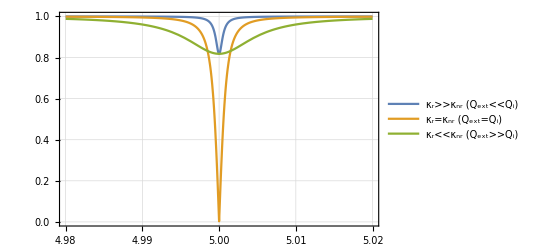

```mathematica
Plot[{Abs[S11Reflection]/.rulesOvercoupled,Abs[S11Reflection]/.rulesCritcoupled,Abs[S11Reflection]/.rulesUndercoupled}, {f, 4.98, 5.02}, PlotRange->{0,1}, PlotTheme->"Detailed", PlotLegends->{"κ_r>>κ_nr (Q_ext<<Q_i)","κ_r=κ_nr (Q_ext=Q_i)", "κ_r<<κ_nr (Q_ext>>Q_i)"}]
```

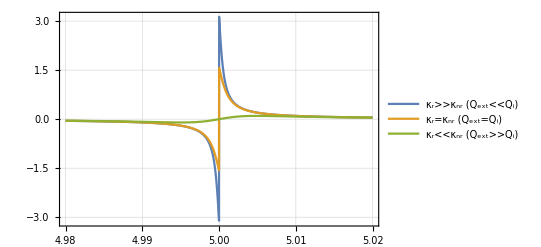

```mathematica
Plot[{Arg[S11Reflection]/.rulesOvercoupled,Arg[S11Reflection]/.rulesCritcoupled,Arg[S11Reflection]/.rulesUndercoupled}, {f, 4.98, 5.02}, PlotRange->{-π,π},  PlotTheme->"Detailed", FrameTicks->{{Automatic  ,Range[-π, π, π/2]},{Automatic,None}}, PlotLegends->{"κ_r>>κ_nr (Q_ext<<Q_i)","κ_r=κ_nr (Q_ext=Q_i)", "κ_r<<κ_nr (Q_ext>>Q_i)"}]
```

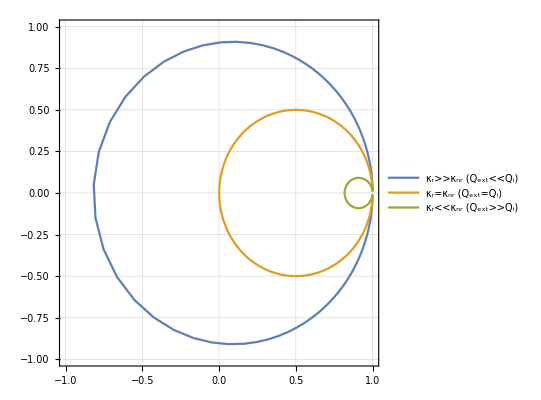

```mathematica
ParametricPlot[{{Re[S11Reflection],Im[S11Reflection]}/.rulesOvercoupled ,{Re[S11Reflection],Im[S11Reflection]}/.rulesCritcoupled ,{ Re[S11Reflection],Im[S11Reflection]}/.rulesUndercoupled },{f, 4.9, 5.1}, PlotRange->{{-1, 1},{-1,1}},  PlotTheme->"Detailed", PlotLegends->{"κ_r>>κ_nr (Q_ext<<Q_i)","κ_r=κ_nr (Q_ext=Q_i)", "κ_r<<κ_nr (Q_ext>>Q_i)"}]
```

```mathematica
S21Transmission=2 Sqrt[κr1 κr2]/(κnr+κr1+κr2+2ⅈ (ω-ω0));
```

```mathematica
ruleFreq=ω->ω0+linew (κr1+κr2);
rulesRightOver={ ω0->2π 5, κr1->2π 0.0015, κr2->2π 0.0005, κnr->2π 0.0002};
rulesRightUnder={ω0->2π 5, κr1->2π 0.0015, κr2->2π 0.0005, κnr->2π 0.02};
rulesRightSame={ω0->2π 5, κr1->2π 0.0015, κr2->2π 0.0005, κnr->2π 0.002};
rulesSameOver={ω0->2π 5, κr1->2π 0.001, κr2->2π 0.001, κnr->2π 0.0002};
rulesSameUnder={ω0->2π 5, κr1->2π 0.001, κr2->2π 0.001, κnr->2π 0.02};
rulesSameSame={ω0->2π 5, κr1->2π 0.001, κr2->2π 0.001, κnr->2π 0.002};

S21Transmission/.ruleFreq/.rulesRightOver
```

0.0108828/(0.013823+(0.+0.0251327 ⅈ) linew)

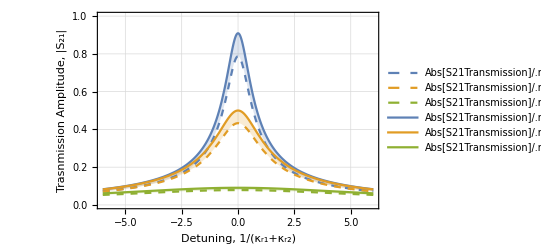

```mathematica
Plot[{Abs@S21Transmission/.ruleFreq/.rulesRightOver,Abs@S21Transmission/.ruleFreq/.rulesRightSame,Abs@S21Transmission/.ruleFreq/.rulesRightUnder,Abs@S21Transmission/.ruleFreq/.rulesSameOver,Abs@S21Transmission/.ruleFreq/.rulesSameSame,Abs@S21Transmission/.ruleFreq/.rulesSameUnder}, {linew,-6,6}, PlotRange->{0,1}, FrameLabel->{"Detuning, 1/(κ_r1+κ_r2)", "Trasnmission Amplitude, |S_21|"}, PlotStyle->{{ColorData[97,"ColorList"][[1]], Dashed},{ColorData[97,"ColorList"][[2]], Dashed},{ColorData[97,"ColorList"][[3]], Dashed},{ColorData[97,"ColorList"][[1]]},{ColorData[97,"ColorList"][[2]]},{ColorData[97,"ColorList"][[3]]}}, Filling->{{1->{4}},{2->{5}},{3->{6}}}, PlotTheme->"Detailed"]
```

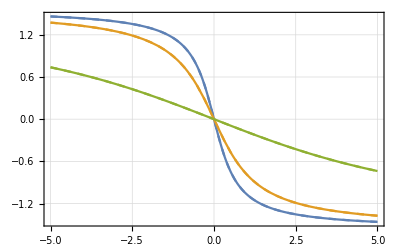

```mathematica
Plot[{Arg@S21Transmission/.ruleFreq/.rulesRightOver,Arg@S21Transmission/.ruleFreq/.rulesRightSame,Arg@S21Transmission/.ruleFreq/.rulesRightUnder,Arg@S21Transmission/.ruleFreq/.rulesSameOver,Arg@S21Transmission/.ruleFreq/.rulesSameSame,Arg@S21Transmission/.ruleFreq/.rulesSameUnder}, {linew,-5,5},PlotStyle->{{ColorData[97,"ColorList"][[1]], Dashed},{ColorData[97,"ColorList"][[2]], Dashed},{ColorData[97,"ColorList"][[3]], Dashed},{ColorData[97,"ColorList"][[1]]},{ColorData[97,"ColorList"][[2]]},{ColorData[97,"ColorList"][[3]]}}, Filling->{{1->{4}},{2->{5}},{3->{6}}}, PlotRange->All, PlotLegends->None,PlotTheme->"Detailed"]
```

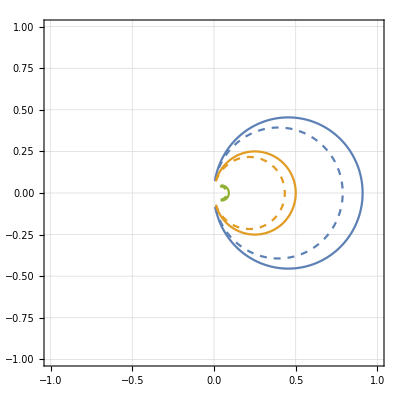

```mathematica
ParametricPlot[{{Re@S21Transmission,Im@S21Transmission}/.ruleFreq/.rulesRightOver,{Re@S21Transmission,Im@S21Transmission}/.ruleFreq/.rulesRightSame,{Re@S21Transmission,Im@S21Transmission}/.ruleFreq/.rulesRightUnder,{Re@S21Transmission,Im@S21Transmission}/.ruleFreq/.rulesSameOver,{Re@S21Transmission,Im@S21Transmission}/.ruleFreq/.rulesSameSame,{Re@S21Transmission,Im@S21Transmission}/.ruleFreq/.rulesSameUnder}, {linew,-6,6},PlotStyle->{{ColorData[97,"ColorList"][[1]], Dashed},{ColorData[97,"ColorList"][[2]], Dashed},{ColorData[97,"ColorList"][[3]], Dashed},{ColorData[97,"ColorList"][[1]]},{ColorData[97,"ColorList"][[2]]},{ColorData[97,"ColorList"][[3]]}},PlotRange->{{-1,1},{-1,1}}, PlotLegends->None, PlotTheme->"Detailed", AspectRatio->Automatic]
```

```mathematica
S21Notch=(κnr+2ⅈ (ω-ω0))/(κnr+κr+2ⅈ (ω-ω0));
```

```mathematica
ruleFreq=ω->ω0+linew (κr);
rulesOvercoupled={ω0->2π 5, κr->2π 0.001, κnr->2π 0.0001};
rulesCritcoupled={ω0->2π 5, κr->2π 0.001, κnr->2π 0.001};
rulesUndercoupled={ω0->2π 5, κr->2π 0.001, κnr->2π 0.01};
```

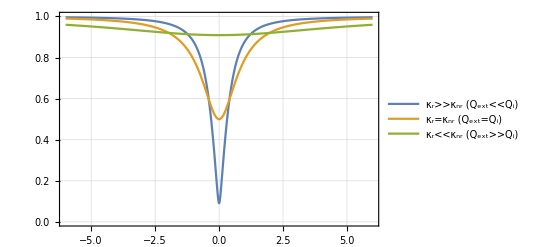

```mathematica
Plot[{Abs[S21Notch]/.ruleFreq/.rulesOvercoupled,Abs[S21Notch]/.ruleFreq/.rulesCritcoupled,Abs[S21Notch]/.ruleFreq/.rulesUndercoupled}, {linew,-6,6}, PlotRange->{0,1}, PlotTheme->"Detailed", PlotLegends->{"κ_r>>κ_nr (Q_ext<<Q_i)","κ_r=κ_nr (Q_ext=Q_i)", "κ_r<<κ_nr (Q_ext>>Q_i)"}]
```

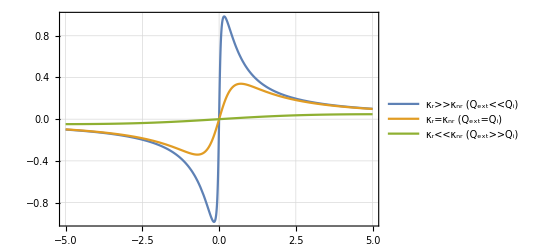

```mathematica
Plot[{Arg[S21Notch]/.ruleFreq/.rulesOvercoupled,Arg[S21Notch]/.ruleFreq/.rulesCritcoupled,Arg[S21Notch]/.ruleFreq/.rulesUndercoupled}, {linew,-5,5}, PlotRange->All, PlotTheme->"Detailed", PlotLegends->{"κ_r>>κ_nr (Q_ext<<Q_i)","κ_r=κ_nr (Q_ext=Q_i)", "κ_r<<κ_nr (Q_ext>>Q_i)"}]
```

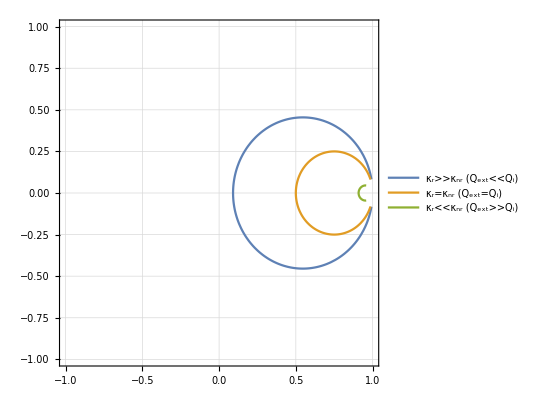

```mathematica
ParametricPlot[{{Re[S21Notch],Im[S21Notch]}/.ruleFreq/.rulesOvercoupled ,{Re[S21Notch],Im[S21Notch]}/.ruleFreq/.rulesCritcoupled ,{ Re[S21Notch],Im[S21Notch]}/.ruleFreq/.rulesUndercoupled },{linew,-6,6}, PlotRange->{{-1, 1},{-1,1}},  PlotTheme->"Detailed", PlotLegends->{"κ_r>>κ_nr (Q_ext<<Q_i)","κ_r=κ_nr (Q_ext=Q_i)", "κ_r<<κ_nr (Q_ext>>Q_i)"}]
```

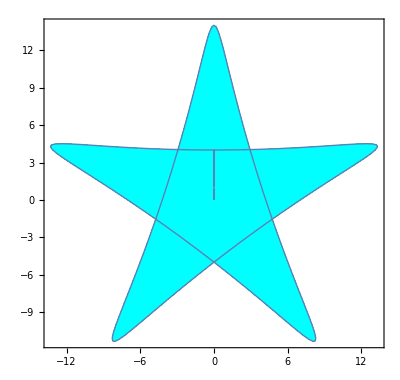

```mathematica
ParametricPlot[u {9 Sin[2 t]+5 Sin[3 t],9 Cos[2 t]-5 Cos[3 t]},{t,0,2 Pi},{u,0,1},MeshFunctions->{Sqrt@(#1^2+#2^2)&},Mesh->{{1}},PlotPoints->30,MeshStyle->Cyan,MeshShading->{Cyan}]
```